# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[ParentDirectory[NotebookDirectory[]]]],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","SemiConstrained","Constrained","ConstrainedCorrelation"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"Bamboo_1","0001",r,"final"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Image sections

```mathematica
dims={412,176}
```

{412,176}

```mathematica
ims=Table[

tim=1;

nx=1+dims[[1]]*tim*i;
ny=1+dims[[2]]*tim*j;

{iaa,ibb,idd,ioo}=ImageTake[#,{ny,ny+dims[[2]]*tim},{nx,nx+dims[[1]]*tim}]&/@{ia,ib,id,io}

,{j,Range[0,0]},{i,Range[0,0]}];

max=MinMax[Flatten[ImageData[idd]]][[2]];
Print["max dv=", max]
ImageDimensions[idd]
```

max dv=38.6009

{413,177}

```mathematica
GraphicsGrid[ims[[All,All,1]],Spacings->-2]
```

-Graphics-

```mathematica
ims=Flatten[ims,1];
```

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## More in depth

```mathematica
ImageDimensions[idd]
```

{413,177}

```mathematica
lvl=1;
```

```mathematica
k=100;
{ka,kd}=ImageData[#][[k]]&/@{iaa,idd};
pyra=pyrFuncGen[ka,lvl];

kb=Table[pyra[[1,1]][x+kd[[x]]],{x,1,1+dims[[1]]*tim}];

pyrb=pyrFuncGen[kb,lvl];


pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
(* Test values *)
testLevels={{1,1}};
e=0.0001;
n=0;
u=0;
steps=1;
```

```mathematica
(* Creating list of initial Values *)
range={-10,0};
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-80];
ListPlot[listv0];
```

```mathematica
(* Creating condition *)
topbot={-10,0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->100];
```

```mathematica
lt=lineTest[n,u,listv0,condition,Range[1,dims[[1]]],pyrab[[1;;1]],e,"ConstrainedCorrelation"];
```

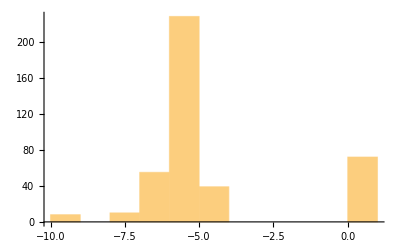

```mathematica
Histogram[Total[#]&/@lt[[All,1;;2]]]
```

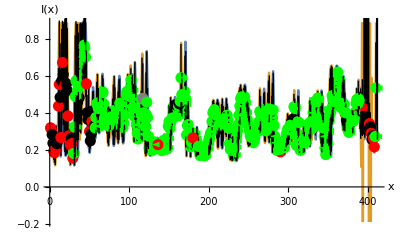

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,dims[[1]]*tim],pyrab[[1;;1]],e,"ConstrainedCorrelation"]
```

```mathematica
(*pixelIterGraphics[10,1,0,20,{{0.,0.}},condition,5, 1,pyrab[[1;;1]],e,"ConstrainedCorrelation"]*)
```

## Little functions

```mathematica
(*[steps,n,u,listv0,condition,e,{levels},ims]*)
bigTest[steps_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
depth=stereoDepth[n,u,listv0,condition,im[[1]],im[[2]],minmax[[2]],minmax,Range[1,1+dims[[1]]*tim,steps],Range[1,1+dims[[2]]*tim],e,"ConstrainedCorrelation"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We create g0 *)
g0=Graphics[{PointSize[0.003],Table[affiche[#,1+dims[[2]]*tim-y]&/@realPVTable[[y]],{y,1,1+dims[[2]]*tim}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Run

```mathematica
Print["minmax dv=",MinMax[Flatten[ImageData[id]]]]
```

minmax dv={0.136895,38.6009}

```mathematica
(* Test values *)
levels={{1,1}};
e=0.0001;
n=0;
u=0;
steps=1;
```

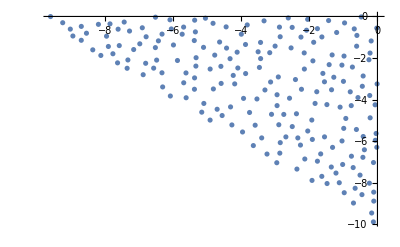

```mathematica
(* Creating list of initial Values *)
range={-10(**0.1*),0};
listv0=Select[RandomReal[range,{3000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-200];
ListPlot[listv0]
```

```mathematica
(* Creating condition *)
topbot={-10(**0.1*),0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
solution = bigTest[steps,n,u,listv0,condition,e,levels,ims];
```

```mathematica
Print["levelTable Dimensions=",Dimensions[solution]]
```

levelTable Dimensions={1,1,4}

```mathematica
solution[[1,1,1,6]]
```

{{90.1258,-9.76745},{89.6885,-9.67202},{88.465,-9.61882},{88.3529,-9.61776},{89.7439,-9.69435},{90.7544,-9.97812},{113.492,-5.46519},{113.586,-5.42282},{113.253,-5.49026},{120.102,-5.48437},{120.558,-5.47812},{120.883,-5.46606},{120.844,-5.46824},{121.044,-5.45328},{121.156,-5.44188},{122.292,-5.52468},{126.811,-5.51313},{127.115,-5.51047},{127.109,-5.51026},{126.871,-5.50953},{126.669,-5.51783},{132.292,-5.45886},{132.047,-5.6959},{130.718,-5.30962},{130.437,-5.46856},{136.003,-5.45575},{136.39,-5.4351},{136.182,-5.44869},{135.606,-5.45376},{135.463,-5.45039},{140.395,-5.19882},{140.094,-5.69206},{139.971,-5.79577},{140.102,-5.70346},{145.141,-6.14448},{147.215,-6.10768},{147.929,-6.19502},{147.976,-6.19966},{147.979,-6.19893},{148.206,-6.20848},{147.975,-6.19709},{154.087,-6.18686},{153.671,-6.21303},{153.618,-6.21623},{153.549,-6.22882},{153.271,-6.26845},{153.384,-6.25172},{154.174,-6.18615},{160.743,-6.2959},{162.16,-6.2271},{162.62,-6.26883},{162.462,-6.26291},{164.886,-6.29719},{164.855,-6.2997},{166.694,-6.39417},{167.906,-6.41796},{164.003,-6.29319},{164.048,-6.30256},{168.591,-6.31811},{167.781,-6.41743},{168.157,-6.40205},{168.538,-6.32858},{174.479,-5.92381},{176.692,-6.70181},{174.514,-5.90573},{180.908,-6.57648},{181.048,-6.55638},{180.774,-6.62237},{183.668,-6.5945},{183.767,-6.58962},{186.16,-6.26112},{183.733,-6.59074},{183.478,-6.61203},{183.189,-6.6309},{189.32,-6.22577},{188.959,-6.25187},{188.967,-6.25693},{188.972,-6.25679},{188.849,-6.25806},{195.236,-6.27459},{193.439,-6.24841},{193.817,-6.25561},{194.577,-6.29488},{194.576,-6.29485},{194.378,-6.28378},{200.199,-6.2341},{199.151,-6.25058},{202.995,-6.23122},{203.413,-6.24375},{203.276,-6.2379},{202.859,-6.22776},{202.531,-6.22149},{202.636,-6.22324},{203.148,-6.23211},{212.169,-7.88093},{212.42,-7.87752},{212.573,-7.87603},{212.644,-7.87567},{212.523,-7.87644},{212.366,-7.87947},{212.093,-7.8805},{212.139,-7.89049},{218.033,-8.02442},{216.886,-7.99048},{217.079,-7.99455},{218.261,-8.04258},{218.828,-8.11656},{219.355,-8.22404},{220.526,-7.56035},{220.612,-7.59497},{227.864,-5.49707},{228.585,-5.53773},{228.19,-5.51871},{228.815,-5.47061},{230.984,-5.41504},{229.175,-5.29309},{233.899,-5.28167},{233.914,-5.26253},{231.039,-5.42044},{232.052,-5.54526},{233.393,-5.42063},{238.863,-5.39212},{235.884,-5.47844},{236.541,-5.37174},{241.486,-5.37314},{241.116,-5.40401},{240.644,-5.43089},{240.767,-5.42459},{241.317,-5.38925},{242.955,-5.37302},{243.038,-5.38187},{245.131,-5.31084},{245.089,-5.32678},{250.972,-5.69241},{251.508,-5.65567},{251.607,-5.65088},{251.611,-5.65033},{254.135,-5.44294},{254.487,-5.48775},{257.385,-5.49444},{257.404,-5.5069},{257.149,-5.4793},{256.841,-5.45867},{256.628,-5.43584},{259.959,-5.31625},{259.832,-5.32078},{263.155,-5.32123},{263.67,-5.33217},{263.461,-5.32588},{263.073,-5.31486},{263.147,-5.31841},{267.741,-5.07106},{268.197,-5.10313},{269.014,-5.37975},{269.299,-5.26882},{269.608,-5.26664},{269.704,-5.26575},{270.194,-5.31826},{271.79,-5.24403},{277.293,-5.7012},{278.351,-5.98788},{279.185,-6.31257},{278.626,-6.09708},{277.813,-5.7805},{278.116,-5.89546},{278.741,-6.13867},{279.354,-6.37778},{285.464,-5.94465},{288.999,-5.40366},{289.338,-5.36156},{289.69,-5.36626},{289.916,-5.37596},{289.85,-5.37459},{289.984,-5.37524},{290.016,-5.3776},{294.569,-4.35325},{294.936,-4.2468},{294.947,-4.24583},{295.015,-4.24638},{295.865,-4.51419},{296.228,-4.70728},{297.036,-5.23498},{302.602,-5.21103},{299.735,-5.01992},{303.108,-5.25561},{304.804,-5.25901},{305.24,-5.2764},{304.867,-5.27243},{308.721,-5.19187},{308.816,-5.1962},{308.614,-5.19927},{308.299,-5.22257},{308.454,-5.21188},{313.68,-5.10352},{310.294,-4.9964},{315.657,-5.1515},{316.282,-5.13059},{316.76,-5.06077},{316.089,-5.13292},{316.709,-5.07095},{317.245,-4.99571},{321.784,-5.1048},{321.723,-5.10799},{321.797,-5.10337},{321.942,-5.10724},{322.004,-5.12934},{324.753,-5.08603},{324.797,-5.0961},{324.758,-5.09375},{325.531,-5.23257},{326.402,-5.07122},{331.433,-5.14826},{332.713,-5.06631},{332.503,-5.04269},{334.836,-5.13187},{335.258,-5.10231},{334.869,-5.13535},{337.902,-5.07842},{338.371,-5.10681},{337.925,-5.07931},{337.169,-5.02747},{341.984,-5.03193},{341.677,-5.00921},{341.214,-5.001},{341.41,-4.99941},{341.541,-5.00659},{346.515,-4.99244},{346.385,-4.9933},{348.187,-4.9763},{346.482,-4.99154},{350.754,-4.94805},{350.202,-4.96792},{352.669,-4.98445},{352.632,-4.98144},{354.659,-5.0012},{354.722,-4.99344},{356.577,-5.02938},{354.666,-4.99878},{354.737,-5.01388},{356.974,-5.01916},{360.775,-4.99982},{360.757,-4.9977},{360.442,-4.99864},{360.603,-4.99928},{360.813,-4.99582},{361.138,-5.00417},{366.294,-4.96944},{366.272,-4.969},{365.879,-4.96456},{365.432,-4.96705},{370.254,-4.9339},{369.912,-4.94108},{369.813,-4.94337},{370.031,-4.93837},{370.514,-4.92813},{375.855,-4.91897},{376.313,-4.88146},{376.995,-4.91609},{377.089,-4.91297},{377.246,-4.92225},{377.075,-4.91594},{377.438,-4.93231},{382.151,-4.80561},{383.522,-4.91061},{383.476,-4.9056},{385.23,-4.91404},{385.302,-4.90988},{385.574,-4.90738},{386.901,-4.87875},{387.452,-4.90624},{387.968,-4.92026},{388.252,-4.93422},{388.642,-4.94355},{389.304,-4.824},{394.833,-4.88628},{395.405,-4.91},{395.68,-4.9092},{395.808,-4.90325},{395.729,-4.91093},{395.731,-4.90865},{397.29,-4.88243},{397.271,-4.88296},{399.014,-5.00433},{403.355,-5.02892},{404.124,-5.00762},{403.335,-5.01514},{403.887,-4.99987},{404.101,-5.00821},{404.128,-5.00505},{409.545,-5.26722}}

### Images

```mathematica
Dimensions[ims]
```

{1,4}

```mathematica
imagesTable=Table[

groundTruth=Image[Table[Map[RainbowColor,imd],{imd,ImageData[Rescale[-ims[[which,3]],scale,{0,1}]]}]];

ConformImages[Rasterize[Image[#],ImageResolution->200]&/@Flatten[{solution[[which,1,4]],groundTruth}],{900}]


,{which,Length[ims]}];
```

```mathematica
im1=GraphicsGrid[Partition[imagesTable[[All,1]],1],Spacings->-2]
im2=GraphicsGrid[Partition[imagesTable[[All,2]],1],Spacings->-2]
```

-Graphics-

-Graphics-

```mathematica
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->100];
```

```mathematica
imFinal=Legended[GraphicsRow[{im1,im2},ImageSize->Large,Spacings->-25],legendBar]
```

-Graphics-

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"fullSintelDataset"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],Rasterize[imFinal,ImageSize->500,ImageResolution->200]]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\fullSintelDataset\sintel-bamboo-final-Full-im.pdf

### More numbers

```mathematica
fontsize=16;
```

```mathematica
numbersTable=Table[

groundTruth=ImageData[-ims[[which,3]]];
solution[[which,1,1]];

density=(Length[Flatten[DeleteDuplicates[#]&/@Floor[solution[[which,1,1,All,All,1]]]]])/((1.+dims[[1]]*tim)*(1.+dims[[2]]*tim));

vals=Table[
ps=Select[solution[[which,1,1,y,All,All]],1<Round[#[[1]]]<(1.+dims[[1]]*tim)&];
(ps[[All,2]]-groundTruth[[y,Round[ps[[All,1]]]]])^2

,{y,Length[solution[[which,1,1]]]}];

rmse=Sqrt[Mean[Flatten[vals]]];

{Style["RMSE= ",FontSize->fontsize,FontFamily->"Times",Italic],rmse,Style["Density= ",FontSize->fontsize,FontFamily->"Times",Italic],density}

,{which,Length[ims]}]
```

{{RMSE= ,2.87835,Density= ,0.316754}}

### Histogram

```mathematica
fontsize=30;
imagesize=500;
maxvalue={{-10.2,1},{0,10000}};
```

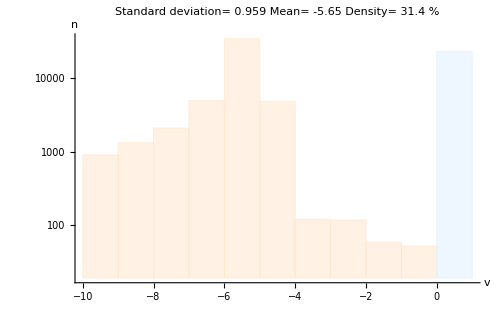

```mathematica
histogramGrid=
Table[

convergedData=Flatten[solution[[idxims,1,1,All,All,2]]];
okData=Flatten[solution[[idxims,1,2,All,All,2]]];
nonConvergedData=Flatten[solution[[idxims,1,3,All,All,2]]];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=((Length[Flatten[DeleteDuplicates[#]&/@Round[solution[[idxims,1,1,All,All,1]]]]])/((1.+dims[[1]]*tim)*(1.+dims[[2]]*tim)))*100;

Histogram[{convergedData, nonConvergedData},10,"LogCount",
PlotLabel->Column[{
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density,3]," %"}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},ChartStyle->{LightOrange,LightBlue,LightGreen},TicksStyle->fontsize-6]
,{idxims,Length[ims]}]
```

```mathematica
dims[[1]]*dims[[2]];
Dimensions[convergedData];
```

```mathematica
convergedData=Select[Flatten[ImageData[-ims[[1,3]]]], topbot[[1]]<#<topbot[[2]]&];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=(Dimensions[convergedData][[1]]/(dims[[1]]*dims[[2]]))*100.;
```

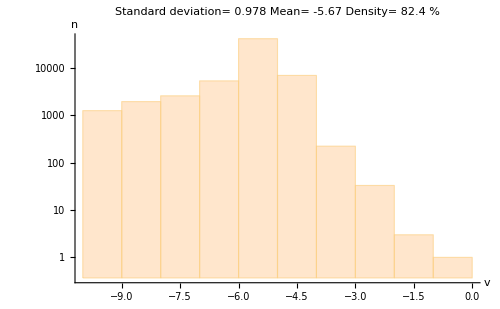

```mathematica
hGroundTruth=Histogram[convergedData,10,"LogCount",
PlotLabel->Column[{
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density,3]," %"}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},
ChartStyle->{LightOrange},TicksStyle->fontsize-6]
```

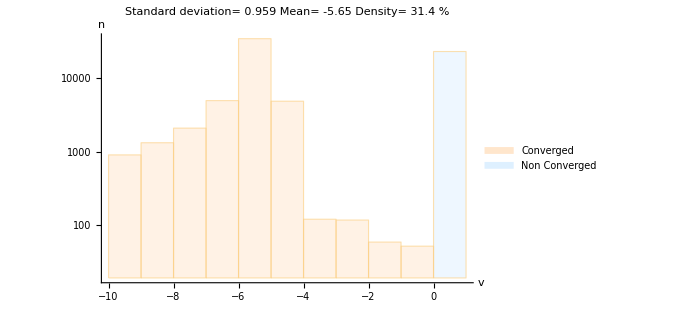
-Graphics--Graphics-

```mathematica
hFinal=Legended[
Row[{histogramGrid[[1]],hGroundTruth}],
Placed[SwatchLegend[{LightOrange, LightBlue, LightGreen},{Style["Converged",FontSize->fontsize, FontFamily->"Times",Italic], Style["Non Converged",FontSize->fontsize, FontFamily->"Times",Italic]},LegendLayout->"Row"],Below]]
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"fullSintelDataset"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-his.pdf"}],Rasterize[hFinal,ImageSize->500,ImageResolution->200]]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\fullSintelDataset\sintel-bamboo-final-Full-his.pdf